-(3 ⅇ^(6 v) (9+1-(ⅇ+ⅇ^2+ⅇ^3+ⅇ^4+ⅇ^5+ⅇ^6+ⅇ^7+ⅇ^8+ⅇ^9+ⅇ^11+ⅇ^12)/(ⅇ+ⅇ^2+ⅇ^3+ⅇ^4+ⅇ^5+ⅇ^6+ⅇ^7+ⅇ^8+ⅇ^9+ⅇ^10+ⅇ^11+ⅇ^12+ⅇ^13+ⅇ^14)))/((ⅇ^3+ⅇ^6+ⅇ^9+ⅇ^12+ⅇ^18+ⅇ^21+ⅇ^24+ⅇ^27+ⅇ^30+ⅇ^33+ⅇ^36+ⅇ^39+ⅇ^42+ⅇ^(3 v))^2)+231+(3 ⅇ^(3 v) (1))/(ⅇ^3+ⅇ^6+ⅇ^9+ⅇ^12+ⅇ^18+ⅇ^21+ⅇ^24+ⅇ^27+ⅇ^30+ⅇ^33+ⅇ^36+ⅇ^39+ⅇ^42+ⅇ^(3 v))
 |  |  |  |

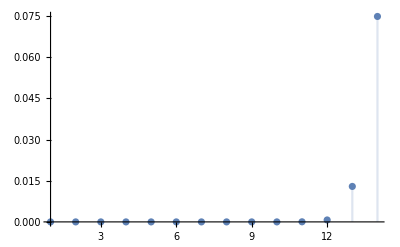

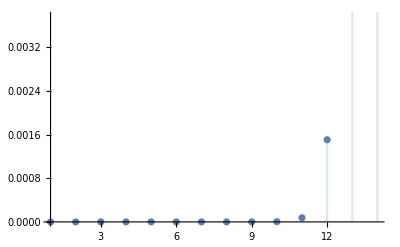

```mathematica
k = 3;
beta1=1;
beta2 = 3;
choicesets = Subsets[Range[14],{k}];
s1=RandomSample[Range[14]];
s2=RandomSample[Range[14]];
innerSum[cs_,sub_,s1_,beta_]:=(-1)^Length[sub]*Total[Exp[beta*s1[[Complement[Range[14],cs]]]]]/(Total[Exp[beta*s1[[Complement[Range[14],cs]]]]]+Total[Exp[beta*s1[[sub]]]])
probOfCS [cs_,s1_,beta_]:=Sum[innerSum[cs,Subsets[cs][[i]],s1,beta],{i,Length[Subsets[cs]]}]
probSelection[q_,s2_,beta_]:=Exp[beta*s2[[q]]]/Total[Exp[beta*s2]]
f[q_,choicesets_,s1_,s2_,beta1_,beta2_]:=Sum[probOfCS[choicesets[[i]],s1,beta1]* Boole[MemberQ[choicesets[[i]],q]]*probSelection[q,s2,beta2],{i,Length[choicesets]}]
(*DiscretePlot[f[1,choicesets,s1,ReplacePart[s2,1->v],beta],{v,1,14}]*)

D[f[1,choicesets,s1,ReplacePart[s2,1->v],beta1,beta2],v]
DiscretePlot[Evaluate[D[f[1,choicesets,s1,ReplacePart[s2,1->v],beta1,beta2],{v,1}]],{v,1,14},PlotRange->Full]
```

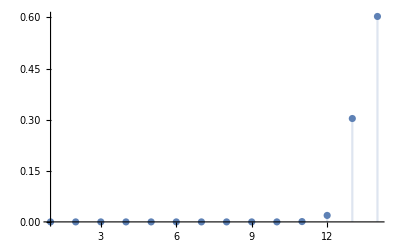

```mathematica
fmix[q_,s1_,s2_,beta1_,beta2_]:=Exp[beta1*s1[[q]]+beta2*s2[[q]]]/Total[Exp[beta1*s1+beta2*s2]]
DiscretePlot[Evaluate[D[fmix[1,s1,ReplacePart[s2,1->v],beta1,beta2],{v,1}]],{v,1,14},PlotRange->Full]
```